```mathematica
CirclInterArea[{r1_, x1_, y1_}, { r2_, x2_, y2_}] := Module[{disk1, disk2, intersec},
disk1 = Disk[{x1, y1}, r1];
disk2 = Disk[{x2, y2}, r2];
intersec = RegionIntersection[disk1, disk2];
Return[N@Area[intersec]]
]
```

```mathematica
CirclInterArea[{1, 0, 0 }, {2, 1, -1}] (*two circles*)
```

2.55607

```mathematica
Manipulate[{RegionPlot[{Disk[{x1, y1}, r1], Disk[{x2, y2}, r2]}, PlotRange->{{-7, 7}, {-7, 7}}], CirclInterArea[{r1, x1, y1}, {r2, x2, y2}]},
 {{r1, 1}, 0, 5}, {{r2, 1}, 0, 5},{{x1, 0}, -5, 5},{{x2, 0}, -5, 5},{{y1, 0}, -5, 5},{{y2, 0}, -5, 5}]
```

```mathematica
RowCircInter[{r1_, x1_, y1_}, {r2_, d_}] := Module[{xBeg = Floor[x1, d], xMin, xMax, CircTable, pipeCircl},
xMin = xBeg - (Mod[d, r1])*d;
xMax = xBeg +(Mod[r1, d]) * d;
CircTable = Table[Disk[{x, 0}, r2], {x, xMin, xMax, d}];
pipeCircl = Disk[{x1, y1}, r1];
Area@RegionIntersection[RegionUnion@CircTable,pipeCircl ]
]
```

```mathematica
Manipulate[RowCircInter[{2, x, 0.5}, {2, 5}], {x, -100, 100}]
```

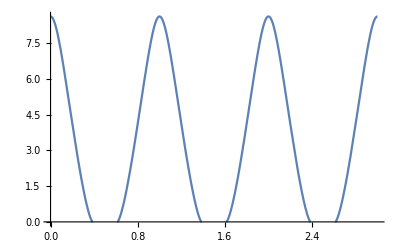

```mathematica
Plot[RowCircInter[{2, 10t, 1}, {2, 10}], {t, 0, 3}]
```

```mathematica
Play[RowCircInter[{2, 1000t, 1}, {2, 10}], {t, 0, 3}]
```

$Aborted

```mathematica
animation = Animate[Module[{diskInn1, diskInn2, intersection}, 
diskInn1 = Disk[{0, 0}, 2];
diskInn2 = Disk[{x, 0}, 1];
intersection = RegionIntersection[diskInn1, diskInn2];
(*RegionPlot[{diskInn1, diskInn2, intersection}, PlotRange->{{-4, 4}, {-4, 4}}]*)
Show[RegionPlot[diskInn1, PlotStyle -> White],RegionPlot[diskInn2 , PlotStyle->White],RegionPlot[intersection, PlotStyle->RGBColor[0.0, 1, 1]],  PlotRange -> {{-4, 4}, {-4, 4}}]
], {x, -4, 4, 0.03}, AnimationDirection->ForwardBackward]
```

```mathematica
Export["/home/kenlog_new/Pictures/circles_animation.gif",animation, "ControlAppearance"->None,"AnimationRepetitions"->Infinity,"AnimationRate"->Automatic,"DisplayDurations"->1/10]
```

/home/kenlog_new/Pictures/circles_animation.gif

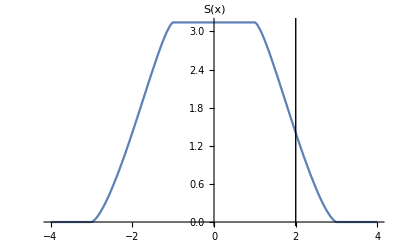

```mathematica
plot = Plot[CirclInterArea[{2, 0,0}, {1,x,0}], {x, -4, 4}, PlotRange->Full, AxesLabel->S[x]]
```

```mathematica
animationPlot = Animate[Show[ plot , Epilog->Line[{{a,-1},{a,4}}]], {a, -4, 4}]
```

```mathematica
Export["/home/kenlog_new/Pictures/circles_animation_plot.gif",animationPlot, "ControlAppearance"->None,"AnimationRepetitions"->Infinity,"AnimationRate"->Automatic,"DisplayDurations"->1/10]
```

/home/kenlog_new/Pictures/circles_animation_plot.gif